## Solving for omega (inverse transformation)

```mathematica
phimat = RotationMatrix[phi,{0,0,1}];
chimat = RotationMatrix[chi,{1,0,0}];
omegamat = RotationMatrix[omega,{0,0,1}];
pitchmat = RotationMatrix[pitch,{0,1,0}];
totmat = pitchmat.omegamat.chimat.phimat
```

{{Cos[omega] Cos[phi] Cos[pitch]+Sin[phi] (-Cos[chi] Cos[pitch] Sin[omega]+Sin[chi] Sin[pitch]),-Cos[omega] Cos[pitch] Sin[phi]+Cos[phi] (-Cos[chi] Cos[pitch] Sin[omega]+Sin[chi] Sin[pitch]),Cos[pitch] Sin[chi] Sin[omega]+Cos[chi] Sin[pitch]},{Cos[phi] Sin[omega]+Cos[chi] Cos[omega] Sin[phi],Cos[chi] Cos[omega] Cos[phi]-Sin[omega] Sin[phi],-Cos[omega] Sin[chi]},{-Cos[omega] Cos[phi] Sin[pitch]+Sin[phi] (Cos[pitch] Sin[chi]+Cos[chi] Sin[omega] Sin[pitch]),Cos[omega] Sin[phi] Sin[pitch]+Cos[phi] (Cos[pitch] Sin[chi]+Cos[chi] Sin[omega] Sin[pitch]),Cos[chi] Cos[pitch]-Sin[chi] Sin[omega] Sin[pitch]}}

### Impose Bragg’s law

```mathematica
Qonhead = {qx,qy,qz};
Qinlab = totmat.Qonhead;
Qx = Qinlab[[1]];
Qmag2 = Qinlab.Qinlab;
bragg = (wavelength/2)*Qmag2+Qx//Expand;
(* this will be set to zero later *)
```

### Graphical and root-finding approaches

0.629371-0.32742 Cos[omega]+2.33657 Sin[omega]

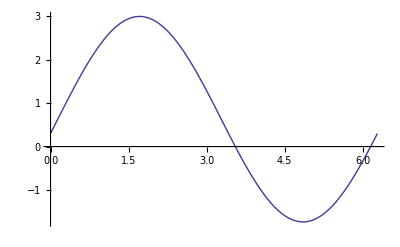

{3.55084,6.15239}

```mathematica
numvals={chi->+20.0(Pi/180),phi->-121.0(Pi/180),pitch->-0.025(Pi/180),wavelength->0.2,qx->2.3,qy->1.0,qz->0};
numbragg = bragg/.numvals/.{Sin[omega]^2->1-Cos[omega]^2}//Simplify
Plot[numbragg,{omega,0,2 Pi}]
solutions = omega/.Solve[numbragg==0,omega]//Mod[#,2Pi]&//Quiet
```

### Direct-calculation approach

```mathematica
nicebragg = numbragg/.{Cos[omega]->c,Sin[omega]->s}
coeff1 = nicebragg/.{c->0,s->0};
coeffc = Coefficient[tempequation,c];
coeffs = Coefficient[tempequation,s];

bias = (coeff1+coeffc2)
phase = ArcTan[coeffc,-coeffs]
amplitude = Sqrt[coeffc^2+coeffs^2]
{1,-1}*ArcCos[-bias/amplitude]-phase//Mod[#,2 Pi]&
```

0.629371-0.32742 c+2.33657 s

0.629371

-1.71002

2.3594

{3.55084,6.15239}